# BigWham Verifications - 3DT6 Kernel

## Spherical cap crack under uniform pressure

### Mesh functions

```mathematica
rk[R_,α_,N_,k_]:=R Sin[k*α/N];
zk[R_,α_,N_,k_]:=R Cos[k*α/N];
MM[R_,α_,N_,k_]:=Round[(2Pi rk[R,α,N,k])/(R α) N ];
StrMB[R_,α_,N_]:=Join[{{0,0,R}},Flatten[Table[{rk[R,α,N,k]Cos[(2π(i-1))/MM[R,α,N,k]],rk[R,α,N,k]Sin[(2π(i-1))/MM[R,α,N,k]],zk[R,α,N,k]},{k,1,N},{i,1,MM[R,α,N,k]}],1]];(*Coordinates of the structured mesh*)
```

```mathematica
MakeSimulation[Radius_,alp_,Meshtype_,Nelcross_]:=(
(*-------Mesh---- *)
pts=StrMB[Radius,alp,Nelcross];
CHM=ConvexHullMesh[pts];
(*-------Points where to get stresses *)
Totalpoints=1;
ObservationPoints2D=Table[{0,0},{i,1,Totalpoints}];
(*PLOTobservationpoints=ListPlot[ObservationPoints2D,PlotStyle->{Directive[Blue,PointSize[Large]]}];*)
(*-------Get the 3D CARTESIAN coordinates*)
Coordinates=MeshCoordinates[CHM];
(*-------Get the 2D POLAR coordinates*)PLANARCoordinates=Table[{Coordinates[[i]][[1]],Coordinates[[i]][[2]]},{i,1,Length[Coordinates]}];
PolarCoordinates=CoordinateTransform["Cartesian"->"Polar",PLANARCoordinates];(*-------Get the radius of each point*)
Ri=Table[If[ PolarCoordinates[[i]][[1]]< Radius,PolarCoordinates[[i]][[1]],Radius],{i,1,Length[PolarCoordinates]}];
(*-------Get the 2D connectivity*)
temp=MeshCells[CHM,2];
(*LG*)
temp1={{}};
InnerNodes=Table[ptcoord=MeshCoordinates[CHM][[i]];zb=Radius Cos[alp];
If[Abs[ptcoord[[3]]-zb]<10.^-12,0,1],{i,1,Dimensions[MeshCoordinates[CHM],1][[1]]}];
Table[If[Total[InnerNodes[[temp[[i]][[1]]]]]>0.1,AppendTo[temp1,temp[[i]]]];,{i,1,Length[temp]}];
temp=Drop[temp1,1];
(*LG*)
ElementConnectivity=Table[temp[[i]][[1]],{i,1,Length[temp]}];
(*-------Get some mesh informations*)
NumberOfVertexes=Length[Coordinates];
NumberOfElements=Length[ElementConnectivity];
NumberOfNodes=NumberOfElements*6;
NumberOfDDs=NumberOfNodes*3;
(* -------mid side nodes-------*)
maptableforEdges=Table[0,{iin,1,NumberOfVertexes},{jin,1,NumberOfVertexes}];
counter=1;
edgeVSnode={};
ElementVSedges=Table[
If[maptableforEdges[[ElementConnectivity[[element]][[2]]]][[ElementConnectivity[[element]][[3]]]]==0,
maptableforEdges[[ElementConnectivity[[element]][[2]]]][[ElementConnectivity[[element]][[3]]]]=counter;
maptableforEdges[[ElementConnectivity[[element]][[3]]]][[ElementConnectivity[[element]][[2]]]]=counter;
counter=counter+1;
edgeVSnode=Append[edgeVSnode,{ElementConnectivity[[element]][[2]],ElementConnectivity[[element]][[3]]}];
];

If[maptableforEdges[[ElementConnectivity[[element]][[1]]]][[ElementConnectivity[[element]][[3]]]]==0,maptableforEdges[[ElementConnectivity[[element]][[1]]]][[ElementConnectivity[[element]][[3]]]]=counter;
maptableforEdges[[ElementConnectivity[[element]][[3]]]][[ElementConnectivity[[element]][[1]]]]=counter;
counter=counter+1;
edgeVSnode=Append[edgeVSnode,{ElementConnectivity[[element]][[1]],ElementConnectivity[[element]][[3]]}];];

If[maptableforEdges[[ElementConnectivity[[element]][[1]]]][[ElementConnectivity[[element]][[2]]]]==0,maptableforEdges[[ElementConnectivity[[element]][[1]]]][[ElementConnectivity[[element]][[2]]]]=counter;
maptableforEdges[[ElementConnectivity[[element]][[2]]]][[ElementConnectivity[[element]][[1]]]]=counter;
counter=counter+1;
edgeVSnode=Append[edgeVSnode,{ElementConnectivity[[element]][[1]],ElementConnectivity[[element]][[2]]}];];
{maptableforEdges[[ElementConnectivity[[element]][[2]]]][[ElementConnectivity[[element]][[3]]]],
maptableforEdges[[ElementConnectivity[[element]][[1]]]][[ElementConnectivity[[element]][[3]]]],
maptableforEdges[[ElementConnectivity[[element]][[1]]]][[ElementConnectivity[[element]][[2]]]]},{element,1,NumberOfElements}];
(* coordinates of the middle points *)
CoordinatesMiddlePoints=Table[Mean[Coordinates[[edgeVSnode[[i]]]]],{i,1,Length[edgeVSnode]}];
(* Polar Coordinates of the middle points *)
PLANARCoordinatesMiddlePoints=Table[{CoordinatesMiddlePoints[[i]][[1]],CoordinatesMiddlePoints[[i]][[2]]},{i,1,Length[CoordinatesMiddlePoints]}];
PolarCoordinatesMiddlePoints=CoordinateTransform["Cartesian"->"Polar",PLANARCoordinatesMiddlePoints];
(* Radius of the middle points *)RiMiddlePoints=Table[PolarCoordinatesMiddlePoints[[i]][[1]],{i,1,Length[PolarCoordinatesMiddlePoints]}];(* Get the name of the elements at the boundary*)
(ecv=ElementConnectivity)//Short;
(pos=Position[ecv,_?(!FreeQ[#,0|_?Negative]&),{2}])//Short;
ElementsAtBoundary=Table[pos[[i]][[2]],{i,1,Length[pos]}]; 

(* -------z(x,y) position of the OBSERVATION points-------*)
z[{x_,y_}]=0.;
(* -------z(x,y) position of the OBSERVATION points-------*)

(*map the coordinates to the 3rd dimension*)
zObservationPoints=Map[z,ObservationPoints2D];
ObservationPoints3D=Table[Append[ObservationPoints2D[[i]],zObservationPoints[[i]]],{i,1,Length[zObservationPoints]}];

(*-----OBJECT TO BE EXPORTED-----*)
Region3D=GraphicsComplex[Coordinates,Triangle[ElementConnectivity]];
ToBEexported=Graphics3D[Region3D];
(*-----OBJECT TO BE EXPORTED-----*)

(*----PLOTS-----*)
middlepointsplot3D=ListPointPlot3D[CoordinatesMiddlePoints,PlotStyle->{Directive[Red]}];vertexpointsplot3D=ListPointPlot3D[Coordinates,PlotStyle->{Directive[Blue]}];
mesh3DANDnormals=Show[{Table[
{p1,p2,p3}=Coordinates[[ElementConnectivity[[j]]]];
startingPoint=Mean[{p1,p2,p3}];
normal=Cross[p2-p1,p3-p1];
endPoint=startingPoint+0.1*Radius *normal/Norm[normal];Graphics3D[{Arrowheads[{0,.009}],Arrow[{startingPoint,endPoint}]}],{j,1,Length[ElementConnectivity]}]}];
);
MeshINFO[]:=((*Get some mesh informations*)
Print["# Vertexes : ",NumberOfVertexes];
Print["# Elements : ",NumberOfElements];
Print["# Nodes : ",NumberOfNodes];
Print["# DDs : ", NumberOfDDs];)
```

## Load Library

```mathematica
PacletDirectoryLoad[NotebookDirectory[]<>"../../../../"]
<<BigWhamLink`
GetFilesDate[]
```

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/}

BigWhamLink`LTemplate`Classes`

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Thu 18 Feb 2021 22:18:06GMT+1,/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a→Fri 12 Mar 2021 22:21:23GMT+1}

## Mesh

```mathematica
Radius=1.;
alp=ArcSin[0.8/Radius]; (*Angle α as in Fig.*)
Meshtype="Uniform";
Nelcross=10; (*Number of elements along the cross-section.*)
p=1;
MakeSimulation[Radius,alp,Meshtype,Nelcross]
MeshINFO[]
CHM
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

Set::shape: Lists {p1,p2,p3} and {{-0.0465159,-0.798647,0.6},{0.0465159,-0.798647,0.6},{0.0465281,-0.739543,0.6715},{-0.0465281,-0.739543,0.6715}} are not the same shape.

Set::shape: Lists {p1,p2,p3} and {{-0.0465281,-0.739543,0.6715},{0.0465281,-0.739543,0.6715},{0.0461075,-0.674068,0.737229},{-0.0461075,-0.674068,0.737229}} are not the same shape.

Set::shape: Lists {p1,p2,p3} and {{-0.359613,0.0454297,0.931995},{-0.359613,-0.0454297,0.931995},{-0.270869,-0.0452,0.961554},{-0.270869,0.0452,0.961554}} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

# Vertexes : 320

# Elements : 579

# Nodes : 3474

# DDs : 10422

-Graphics3D-

Note : don’t worry about errors poping up from Lisa’s mesh mma code

```mathematica
(* --- for splitting unexpected rectangular elements in two triangles, I don't know why this happens in the mesh coming from Lisa's mesh mma code --- *)

ElementConnectivityAux=ElementConnectivity;
Do[
If[Length@ElementConnectivity[[i]]>3,
ElementConnectivityAux[[i]]=ElementConnectivity[[i,1;;3]];
AppendTo[ElementConnectivityAux,ElementConnectivity[[i,{1,3,4}]]],
ElementConnectivityAux[[i]]=ElementConnectivity[[i]]
]
,{i,1,Length@ElementConnectivity}
];
```

```mathematica
ElementConnectivityAux//Dimensions
```

{584,3}

```mathematica
(* --- renaming --- *)

coorVerticesXYZ=Coordinates;
coorVerticesXYZ//Dimensions
conn=ElementConnectivityAux;
conn//Dimensions
numberElements=Length[conn];
```

{320,3}

{584,3}

## Mesh utilities

### Rotation matrices

```mathematica
computeRotationMatrix[y1_List,y2_List,y3_List]:=Module[
{tangent1,normal,tangent2,rotMat},
tangent1=y2-y1;
tangent1=tangent1/Norm[tangent1];
normal=Cross[tangent1,y3-y1];
normal=normal/Norm[normal];
tangent2=Cross[normal,tangent1];
rotMat={tangent1,tangent2,normal}
];

allRotMat=Table[
computeRotationMatrix[
coorVerticesXYZ[[conn[[i,1]]]],
coorVerticesXYZ[[conn[[i,2]]]],
coorVerticesXYZ[[conn[[i,3]]]]],
{i,numberElements}];
```

## Build H-mat

```mathematica
ker="3DT6";
G=1.;ν=0.25;Young=2G(1+ν);(*λ=(Young ν)/((1+ν)(1-2 ν));*)
maxleaf=100;
eta=5.;
eps=0.0001;
```

```mathematica
h1=toHMatExpr[coorVerticesXYZ,conn,ker,{Young,ν},maxleaf,eta,eps];//AbsoluteTiming
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

{198.474,Null}

```mathematica
GetCompressionRatio[h1]
GetSize[h1]
numberUnknowns=GetSize[h1][[1]]
numberCollocationPoints=numberUnknowns/3
```

0.351656

{10512,10512}

10512

3504

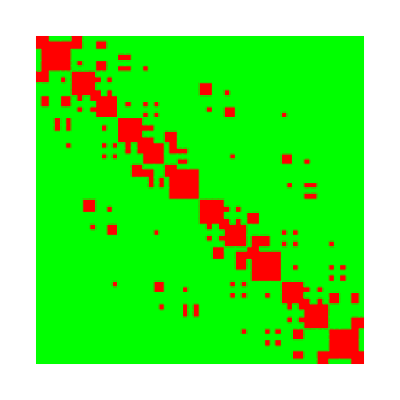

```mathematica
PlotHpattern[h1]
```

## Verification

### Import AxiDDM solution

```mathematica
DDnormalAxiDDM=Import[NotebookDirectory[]<>"Un.csv","csv"]//Flatten;
DDshearAxiDDM=Import[NotebookDirectory[]<>"Us.csv","csv"]//Flatten;
radialCoorAxiDDM=Import[NotebookDirectory[]<>"Rm.csv","csv"]//Flatten;
```

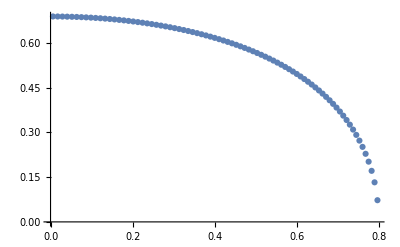

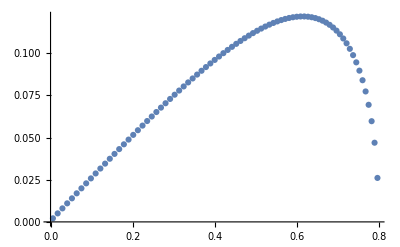

```mathematica
ListPlot[{radialCoorAxiDDM,DDnormalAxiDDM}//Transpose]
ListPlot[{radialCoorAxiDDM,DDshearAxiDDM}//Transpose]
```

### Numerical solution via BigWham 3DT6

#### Nodes for 3DT6

```mathematica
(* --- coordinates of nodes for 3DT6 --- *)

computeNodesCoordinates[y1_List,y2_List,y3_List]:=Module[
{coorNodes},
coorNodes=ConstantArray[0.,{6,3}];
coorNodes[[1]]=y1;coorNodes[[2]]=y2;coorNodes[[3]]=y3;
(*Same convention that C++ for middle edge nodes*)
coorNodes[[4]]=(y2+y3)/2;
coorNodes[[5]]=(y1+y3)/2;
coorNodes[[6]]=(y1+y2)/2;
coorNodes
];
coorNodesXYZ=Table[
computeNodesCoordinates[
coorVerticesXYZ[[conn[[i,1]]]],
coorVerticesXYZ[[conn[[i,2]]]],
coorVerticesXYZ[[conn[[i,3]]]]],
{i,numberElements}];
coorNodesXYZ=Flatten[coorNodesXYZ,1];
```

#### Collocation points

```mathematica
(* --- collocation points for any kernel --- *)
(* be careful, they are permuted !! *)

coorCollXYZ=GetCollocationPoints[h1];
```

```mathematica
Show[Graphics3D[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXYZ,Polygon[conn]]}],
ListPointPlot3D[coorCollXYZ,PlotStyle-> Red],
ListPointPlot3D[coorNodesXYZ,PlotStyle-> Blue],ImageSize-> 700]
```

-Graphics3D-

## Analytical solution

#### Radial cylindrical coordinate of nodes (DD) and collocation points

```mathematica
rNodes=Norm[#]&/@coorNodesXYZ[[;;,1;;2]];

rColl=Norm[#]&/@coorCollXYZ[[;;,1;;2]];
```

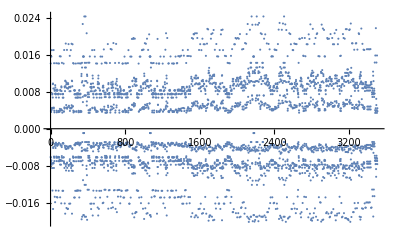

```mathematica
ListPlot[rNodes-rColl,PlotRange->All] (*it's ok, they don't coincide in this case*)
```

### Uniform pressure

```mathematica
P=1;
F=ConstantArray[0.,numberUnknowns];
F[[3;;-1;;3]]=P;
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
```

```mathematica
{sol,stats}=Reap@LinearSolve[fdot,F,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-7.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];//AbsoluteTiming
```

{0.590071,Null}

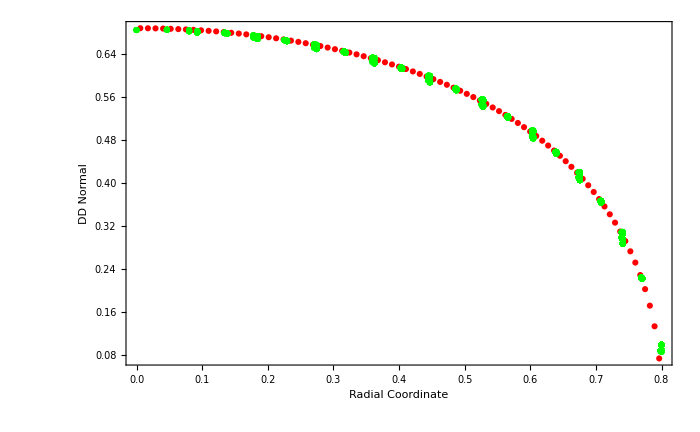

```mathematica
Show[
ListPlot[{radialCoorAxiDDM,DDnormalAxiDDM}//Transpose,PlotMarkers->Automatic,PlotStyle->Red],
ListPlot[{rNodes,sol[[3;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Green],
Frame-> True,BaseStyle->{FontColor->Black,FontSize->22,FontFamily->"Times"},
FrameLabel->(Style[#,FontColor->Black,FontSize->25]& /@{"Radial Coordinate","DD Normal"}), 
PlotRange-> All,ImageSize-> 700,PlotRange-> All]
```

```mathematica
(* --- shear DD --- *)
(* as the problem is axisymmetric, we compute the maximum shear DD that should happen in the radial direction*)

DDshearBigWham=Norm[#]&/@({sol[[1;;-1;;3]],sol[[2;;-1;;3]]}//Transpose);
```

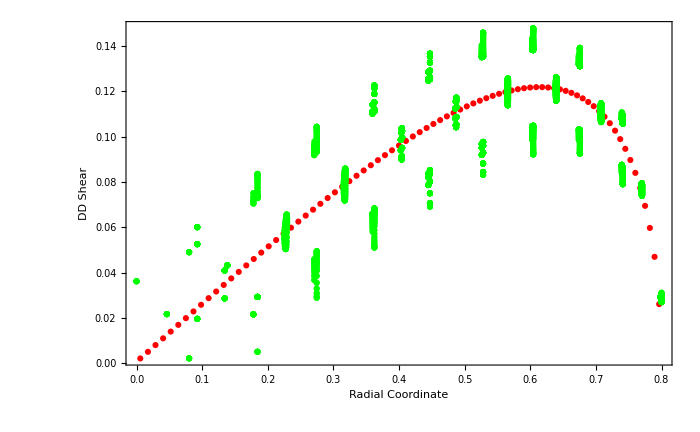

```mathematica
Show[
ListPlot[{radialCoorAxiDDM,DDshearAxiDDM}//Transpose,PlotMarkers->Automatic,PlotStyle->Red],
ListPlot[{rNodes,DDshearBigWham}//Transpose,PlotMarkers->Automatic,PlotStyle->Green],
Frame-> True,BaseStyle->{FontColor->Black,FontSize->22,FontFamily->"Times"},
FrameLabel->(Style[#,FontColor->Black,FontSize->25]& /@{"Radial Coordinate","DD Shear"}), 
PlotRange-> All,ImageSize-> 700,PlotRange-> All]
```